## QED Renormalization at 1-loop

This example uses custom QED model created with FeynRules. Please evaluate the file
FeynCalc/Examples/FeynRules/QED/GenerateModelQED.m before running it for the first time

```mathematica
Quit[]
```

### Load FeynCalc, FeynArts and FeynHelpers

```mathematica
If[ $FrontEnd === Null,
		$FeynCalcStartupMessages = False;
		Print["Computation of the renormalization constants at 1-loop"];
];
$LoadAddOns={"FeynArts","FeynHelpers"};
Import[NotebookDirectory[]<>"FeynCalc/FeynCalc.m"]
$FAVerbose = 0
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

0

### Important options

```mathematica
FAPatch[PatchModelsOnly->True];
$KeepLogDivergentScalelessIntegrals=True;
SetOptions[FourVector, FeynCalcInternal -> False];
```

Successfully patched FeynArts.

### Generate the diagrams

```mathematica
params={InsertionLevel->{Particles},Model -> FileNameJoin[{NotebookDirectory[],"FeynCalc","Models","QED","QED"}],
GenericModel -> FileNameJoin[{NotebookDirectory[],"FeynCalc","Models","QED","QED"}],ExcludeParticles->{F[2,{2|3}]}};
top[i_,j_]:=CreateTopologies[1, i -> j,
ExcludeTopologies -> {Tadpoles,WFCorrections,WFCorrectionCTs}];
topCT[i_,j_]:=CreateCTTopologies[1, i ->j,
ExcludeTopologies ->{Tadpoles,WFCorrections,WFCorrectionCTs}];

{diagElectronSE,diagElectronSECT} = InsertFields[#, {F[2,{1}]} -> {F[2,{1}]},
Sequence@@params]&/@{top[1,1],topCT[1,1]};
{diagPhotonSE,diagPhotonSECT} = InsertFields[#, {V[1]} -> {V[1]},
Sequence@@params]&/@{top[1,1],topCT[1,1]};
{diagVertex,diagVertexCT} = InsertFields[#,  {F[2,{1}],V[1]}->{F[2,{1}]},
Sequence@@params]&/@{top[2,1],topCT[2,1]};
```

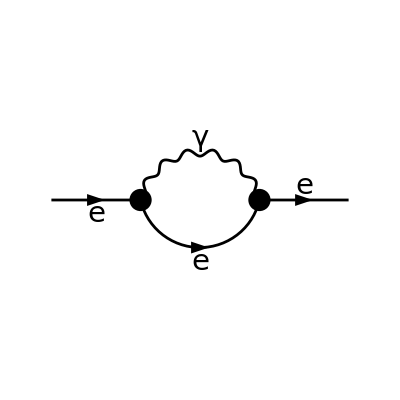

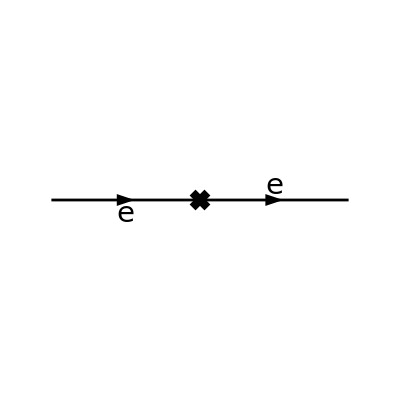

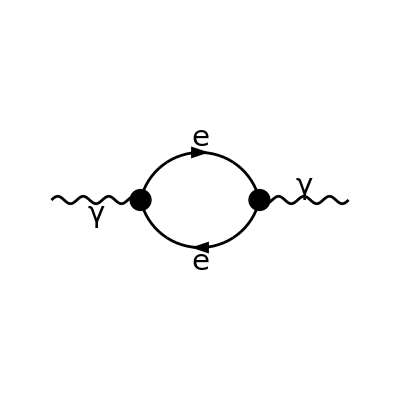

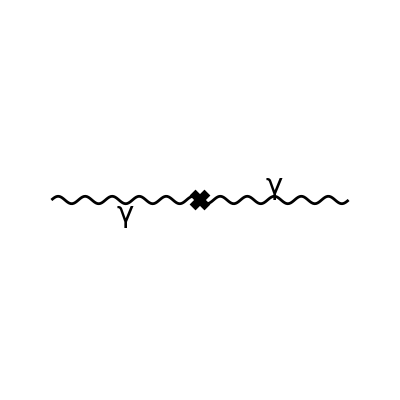

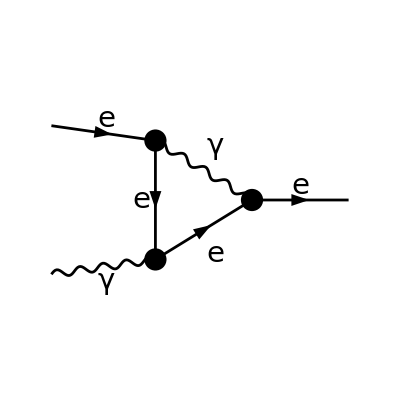

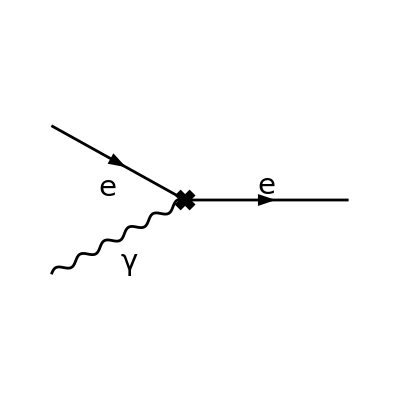

```mathematica
Paint[diagElectronSE, ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{256,256}];
Paint[diagElectronSECT, ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{256,256}];
Paint[diagPhotonSE, ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{256,256}];
Paint[diagPhotonSECT, ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{256,256}];
Paint[diagVertex, ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{256,256}];
Paint[diagVertexCT, ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{256,256}];
```

### Electron self-energy

First of all we need to generate the amplitudes and convert them into FeynCalc notation. We choose l to be the loop momentum and p the external momentum.

```mathematica
FCFAConvert[CreateFeynAmp[diagElectronSE, Truncated -> True,PreFactor->1,
GaugeRules->{}],IncomingMomenta->{p}, OutgoingMomenta->{p},LoopMomenta->{l},DropSumOver->True,
UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->False]//FullForm
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

Times[-2,Power[EL,2],DiracGamma[LorentzIndex[Lor1,D],D],DiracGamma[LorentzIndex[Lor2,D],D],Plus[ME,DiracGamma[Momentum[l,D],D]],PropagatorDenominator[Times[-1,l],ME],PropagatorDenominator[Plus[Times[-1,l],p],0],Plus[Pair[LorentzIndex[Lor1,D],LorentzIndex[Lor2,D]],Times[-1,Plus[1,Times[-1,GaugeXi[V[Index[Generic,4]]]]],Pair[LorentzIndex[Lor1,D],Momentum[Plus[l,Times[-1,p]],D]],Pair[LorentzIndex[Lor2,D],Momentum[Plus[l,Times[-1,p]],D]],PropagatorDenominator[Plus[Times[-1,l],p],0]]]]

```mathematica
{ampElectronSE,ampElectronSECT}=Contract[FCFAConvert[CreateFeynAmp[#, Truncated -> True,PreFactor->1,
GaugeRules->{}],IncomingMomenta->{p}, OutgoingMomenta->{p},LoopMomenta->{l},DropSumOver->True,
UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->False, FinalSubstitutions->{Zm->SMP["Z_m"],
Zpsi->SMP["Z_psi"],SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]]&/@{diagElectronSE,diagElectronSECT}
```

{2 EL^2 PropagatorDenominator(-l,ME) (PropagatorDenominator(p-l,0))^2 (γ·l+ME) (γ·(l-p))^2 (1-ξ_(V(Gen4)))-2 EL^2 (γ^Lor2)^2 PropagatorDenominator(-l,ME) PropagatorDenominator(p-l,0) (γ·l+ME),2 (ⅈ (Z_ψ-1) γ·p-ⅈ ME (Z_m Z_ψ-1))}

Tensor reduction allows us to express the electron self-energy in tems of the Passarino-Veltman coefficient functions.

```mathematica
ampElectronSE1=TID[ampElectronSE,l,ToPaVe->True]//DiracSimplify
```

0

With PaxEvaluateUVIRSplit we obtain the full analytic result for the self-energy diagram

```mathematica
ampElectronSE2=PaXEvaluateUVIRSplit[ampElectronSE1,PaXImplicitPrefactor->1/(2Pi)^D]//Collect2[#,DiracGamma]&//FCHideEpsilon
```

0

This is the amplitude for the self-energy counter-term

```mathematica
ampElectronSECT2=ampElectronSECT//ReplaceAll[#,{SMP["Z_psi"]->1+alpha SMP["d_psi"],
SMP["Z_m"]->1+alpha SMP["d_m"]}]&//Series[#,{alpha,0,1}]&//Normal//ReplaceAll[#,alpha->1]&
```

-2 ⅈ (ME δ_m+ME δ_ψ-δ_ψ γ·p)

Now we add the 1-loop SE diagram and the SE counter-term and discard all the finite pieces

```mathematica
tmp[1]=SelectNotFree2[(ampElectronSECT2+ampElectronSE2),{SMP["Delta_UV"],SMP["Delta_IR"],SMP["d_m"],SMP["d_psi"]}]
```

-2 ⅈ ME δ_m-2 ⅈ ME δ_ψ+2 ⅈ δ_ψ γ·p

Equating our result to zero and solving for d_psi and d_m we obtain  the renormalization constants in the minimal subtraction schemes.

```mathematica
sol[1]=Solve[SelectNotFree2[tmp[1], DiracGamma]==0,SMP["d_psi"]]//Flatten//Simplify;
sol[2]=Solve[(SelectFree2[tmp[1], DiracGamma]==0)/.sol[1],SMP["d_m"]]//Flatten//Simplify;
solMS=Join[sol[1],sol[2]]/.{SMP["d_psi"]->SMP["d_psi^MS"],SMP["d_m"]->SMP["d_m^MS"],SMP["Delta_UV"]->1/EpsilonUV}
solMSbar=Join[sol[1],sol[2]]/.{SMP["d_psi"]->SMP["d_psi^MSbar"],SMP["d_m"]->SMP["d_m^MSbar"]}
```

{δ_ψ^MS→0,δ_m^MS→0}

{δ_ψ^(MS^—)→0,δ_m^(MS^—)→0}

For the on-shell scheme it is convenient to define the scalar product p.p as psq, since we will need to expand in this quantity

```mathematica
FCClearScalarProducts[];
SPD[p,p]=psq;
```

It is also convenient to split the self-energy into a scalar (SigmaS) and a vector (SigmaV) part.

```mathematica
SigmaS=Simplify[Cancel[SelectFree2[ampElectronSE1,DiracGamma]/(SMP["m_e"]I)]]
```

0

```mathematica
SigmaV=Simplify[Cancel[SelectNotFree2[ampElectronSE1,DiracGamma]/(FCI[GSD[p]]I)]]
```

0

According to the on-shell renormalization condition, the mass renormalization constant is given by the sum of SigmaS and SigmaV evaluated at p.p =0

```mathematica
solOS={SMP["d_m^OS"]->FCHideEpsilon[PaXEvaluateUVIRSplit[SigmaS+SigmaV,PaXImplicitPrefactor->1/(2Pi)^D,
PaXSeries->{{psq,SMP["m_e"]^2,0}},PaXAnalytic->True,FCVerbose->0]]//
FCFactorOut[#,(-3/(4Pi)SMP["alpha_fs"])]&}
```

{δ_m^OS→0}

For the wave-function renormalization constant we need the derivative of SigmaS+SigmaV evaluated at p.p=0

```mathematica
tmp[2]=Simplify[(PaXEvaluateUVIRSplit[SigmaS+SigmaV,PaXImplicitPrefactor->1/(2Pi)^D,PaXSeries->{{psq,SMP["m_e"]^2,1}},
PaXAnalytic->True,FCVerbose->0]-PaXEvaluateUVIRSplit[SigmaS+SigmaV,PaXImplicitPrefactor->1/(2Pi)^D,
PaXSeries->{{psq,SMP["m_e"]^2,0}},PaXAnalytic->True,FCVerbose->0])/(psq-SMP["m_e"]^2)]//FCHideEpsilon
```

0

as well as SigmaV at p.p=0

```mathematica
tmp[3]=PaXEvaluateUVIRSplit[SigmaV,PaXImplicitPrefactor->1/(2Pi)^D,
PaXSeries->{{psq,SMP["m_e"]^2,0}},PaXAnalytic->True]//FCHideEpsilon
```

0

Combining both pieces we can determine Subscript[δ, ψ] in the on-shell scheme

```mathematica
aux={SMP["d_psi^OS"]->Simplify[-tmp[3]-2SMP["m_e"]^2 tmp[2]]}
solOS=Union[Join[solOS,aux]];
```

{δ_ψ^OS→0}

### Photon self-energy

Again, first we obtain the amplitudes

```mathematica
{ampPhotonSE,ampPhotonSECT}=FCTraceFactor[Contract[FCFAConvert[CreateFeynAmp[#, Truncated -> True,
PreFactor->1,GaugeRules->{}],IncomingMomenta->{q},OutgoingMomenta->{q},LoopMomenta->{l},
DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,
FinalSubstitutions->{ZA->SMP["Z_A"],Zpsi->SMP["Z_psi"],Zxi->SMP["Z_xi"],
SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]]]&/@{diagPhotonSE,diagPhotonSECT}
```

{-EL^2 γ^Lor1 γ^Lor2 PropagatorDenominator(l,ME) (ME-γ·l) PropagatorDenominator(l-q,ME) (ME-γ·(l-q)),-ⅈ q^2 (Z_A-1) g^Lor1Lor2-(ⅈ q^Lor1 q^Lor2 (Z_A-Z_ξ))/(ξ_(V(1)) Z_ξ)+ⅈ (Z_A-1) q^Lor1 q^Lor2}

then we do the tensor decomposition

```mathematica
ampPhotonSE1=TID[ampPhotonSE,l,ToPaVe->True]
```

0

and finally obtain the explicit results.

```mathematica
ampPhotonSE2=PaXEvaluateUVIRSplit[ampPhotonSE1,PaXImplicitPrefactor->1/(2Pi)^D]//FCHideEpsilon
```

0

This is the counter-term amplitude

```mathematica
ampPhotonSECT2=ampPhotonSECT//ReplaceRepeated[#,{SMP["Z_xi"]->SMP["Z_A"],
SMP["Z_A"]->1+alpha SMP["d_A"]}]&//Normal//ReplaceAll[#,alpha->1]&
```

ⅈ δ_A q^Lor1 q^Lor2-ⅈ q^2 δ_A g^Lor1Lor2

Now we add the 1-loop SE diagram and the SE counter-term and discard all the finite pieces

```mathematica
tmp[4]=(ampPhotonSECT2+ampPhotonSE2)//SelectNotFree2[#,{SMP["Delta_UV"],SMP["d_A"]}]&//Simplify
```

ⅈ δ_A (q^Lor1 q^Lor2-q^2 g^Lor1Lor2)

Equating this to zero and solving for d_A we obtain the wave-function renormalization constant for the photon in the minimal subtraction schemes.

```mathematica
sol[3]=Solve[tmp[4]==0,SMP["d_A"]]//Flatten;
tmp[5]=sol[3]/.{SMP["d_A"]->SMP["d_A^MS"],SMP["Delta_UV"]->1/EpsilonUV}
solMS=Union[Join[solMS,tmp[5]]];
tmp[6]=sol[3]/.{SMP["d_A"]->SMP["d_A^MSbar"]}
solMSbar=Union[Join[solMSbar,tmp[6]]];
```

{δ_A^MS→0}

{δ_A^(MS^—)→0}

```mathematica
SPD[q,q]=qsq;
```

Here we extract Pi(q^2)

```mathematica
tmp[7]=(ampPhotonSE1//Simplify)/(-I FCI[qsq MTD[Lor1,Lor2]-FVD[q,Lor1]FVD[q,Lor2]])
```

0

This is the derivative of  Pi(q^2) evaluated at q^2 = 0

```mathematica
tmp[8]=FCHideEpsilon[(PaXEvaluateUVIRSplit[qsq tmp[7],PaXImplicitPrefactor->1/(2Pi)^D,
PaXSeries->{{qsq,0,1}},PaXAnalytic->True]/qsq)-PaXEvaluateUVIRSplit[qsq tmp3,
PaXImplicitPrefactor->1/(2Pi)^D,PaXSeries->{{qsq,0,0}},PaXAnalytic->True]]
```

0

and from here we obtain d_A in the on-shell scheme

```mathematica
tmp[9]={SMP["d_A^OS"]->-FCFactorOut[tmp[8],SMP["alpha_fs"]/(3Pi)]}
solOS=Union[Join[solOS,tmp[9]]];
```

{δ_A^OS→0}

### Electron-photon vertex

The last piece is the vertex diagram

```mathematica
{ampVertex,ampVertexCT}=Contract[FCFAConvert[CreateFeynAmp[#, Truncated -> True,PreFactor->1,
GaugeRules->{}],IncomingMomenta->{p1,k},OutgoingMomenta->{p2},LoopMomenta->{l},DropSumOver->True,
UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,
FinalSubstitutions->{k->p2-p1,ZA->SMP["Z_A"],Zpsi->SMP["Z_psi"],
Ze->SMP["Z_e"]}]&/@{diagVertex,diagVertexCT}]//ReplaceAll[#,SMP["e"]^3->4Pi SMP["alpha_fs"]SMP["e"]]&
```

{2 EL^3 γ^Lor1 (γ^Lor3)^2 PropagatorDenominator(-l,ME) PropagatorDenominator(p1-l,0) (γ·l+ME) PropagatorDenominator(-l+p1-p2,ME) (ME-γ·(-l+p1-p2))-2 EL^3 γ^Lor1 PropagatorDenominator(-l,ME) (PropagatorDenominator(p1-l,0))^2 (γ·l+ME) (γ·(l-p1))^2 (1-ξ_(V(Gen5))) PropagatorDenominator(-l+p1-p2,ME) (ME-γ·(-l+p1-p2)),2 ⅈ EL γ^Lor1 (√Z_A Z_e Z_ψ-1)}

The result of the tensor reduction is quite large, since we keep the full gauge dependence and do not specify the kinematics

```mathematica
ampVertex1=TID[ampVertex,l,ToPaVe->True,UsePaVeBasis->True]
```

0

As we are interested in the UV piece only, there is no need to obtain the full analytic result

```mathematica
tmp[10]=PaXEvaluateUV[ampVertex1,PaXImplicitPrefactor->1/(2Pi)^D]
```

0

This is the amplitude from the counter-term vertex

```mathematica
ampVertexCT2=Normal[Series[ampVertexCT/.{SMP["Z_A"]->1+alpha SMP["d_A"],
SMP["Z_e"]->1+alpha SMP["d_e"],SMP["Z_psi"]->1+alpha SMP["d_psi"]},{alpha,0,1}]]/.alpha->1
```

2 ⅈ EL γ^Lor1 (δ_A/2+δ_ψ+δ_e)

Adding both amplitudes and equating them to zero gives

```mathematica
tmp[11]=(Cancel[(tmp[10]+ampVertexCT2)/(-FCI [I SMP["e"] GAD[Lor1]])]//Simplify)==0
```

-(EL (δ_A+2 (δ_ψ+δ_e)))/e==0

After plugging in d_Psi and d_m that were determined previously, we can confirm Ward's identity which fixes the relation between d_A and d_e

```mathematica
Simplify[tmp[11]/.{SMP["d_psi"]->SMP["d_psi^MS"]}/.solMS]
```

(EL (δ_A+2 δ_e))/e==0

```mathematica
Simplify[tmp[11]/.EpsilonUV->1/SMP["Delta_UV"]/.{SMP["d_psi"]->SMP["d_psi^MSbar"]}/.solMSbar]
```

(EL (δ_A+2 δ_e))/e==0

Finally, we want to look at the vertex in the on-shell scheme

```mathematica
FCClearScalarProducts[];
SPD[p1,p1]=SMP["m_e"]^2;
SPD[p2,p2]=SMP["m_e"]^2;
```

Here we sandwich the amplitude between two spinors with 4-momenta p1 and p2.

```mathematica
tmp[12]=SpinorUBarD[p2,SMP["m_e"]] . ampVertex . SpinorUD[p1,SMP["m_e"]]//TID[#,
l,UsePaVeBasis->True,ToPaVe->True]&//DiracSimplify;
```

DotSimplify::failmsg: Error! DotSimplify has encountered a fatal problem and must abort the computation. The problem reads: Detected commutative multiplication of noncommutative objects.

$Aborted

Collecting the terms

```mathematica
tmp[13]=(ExpandScalarProduct[tmp[12]]/.FCI@FVD[p1,Lor1]->FCI[FVD[p1p2,Lor1]-FVD[p2,Lor1]])//
Collect2[#,LorentzIndex]&
```

tmp(12)

and applying Gordon decomposition we can bring the expression to the form dictated by the Lorentz covariance.

```mathematica
tmp[14]=(1/(SMP["e"] I)tmp[13]/.{FCI[FVD[p1p2,i_]SpinorUBarD[p2,m_] . SpinorUBarD[p1,m_]]:>
FCI[SpinorUBarD[p2,m] . (2m GAD[i]-I DiracSigma[GAD[i],GSD[p2-p1]]) . SpinorUD[p1,m]]})//
DotSimplify//Collect2[#,LorentzIndex]&;
```

This is  F_2(0)

```mathematica
tmp[15]=Simplify[SelectNotFree2[tmp[14],DiracSigma]/
FCI[I/(2SMP["m_e"])SpinorUBarD[p2,SMP["m_e"]] . DiracSigma[GAD[Lor1],GSD[p2-p1]] . SpinorUBarD[p1,SMP["m_e"]]]]
```

0

its explicit value reproduces the beautiful result by Schwinger for (g-2)/2

```mathematica
PaXEvaluateUVIRSplit[tmp[15]/.{FCI[SPD[p1,p2]]->SMP["m_e"]^2},PaXImplicitPrefactor->1/(2Pi)^D]
```

0

We need F_1(0) to recover the on-shell renormalization condition

```mathematica
tmp[16]=Cancel[DotSimplify[(tmp[14]/.p2->p1)]/FCI[SpinorUBarD[p1,SMP["m_e"]] . GAD[Lor1] . SpinorUD[p1,SMP["m_e"]]]]
```

-(ⅈ tmp(12))/(e (φ(p1,m_e)).γ^Lor1.(φ(p1,m_e)))

```mathematica
tmp[17]=PaXEvaluateUVIRSplit[tmp[16],PaXImplicitPrefactor->1/(2Pi)^D,PaXAnalytic->True]//FCHideEpsilon
```

-(ⅈ tmp(12))/(16 π^4 e (φ(p1,m_e)).γ^Lor1.(φ(p1,m_e)))

Adding things up we again confirm Ward's identity, this time in the on-shell scheme

```mathematica
Simplify[((tmp[17]+(ampVertexCT2/(I SMP["e"]FCI[GAD[Lor1]])))/.{SMP["d_psi"]->SMP["d_psi^OS"]}/.solOS)==0]
```

(-(ⅈ tmp(12))/((φ(p1,m_e)).γ^Lor1.(φ(p1,m_e)))+16 π^4 EL δ_A+32 π^4 EL δ_e)/e==0

At the end we summarize our results

```mathematica
solOS//TableForm
```

δ_A^OS→0
δ_m^OS→0
δ_ψ^OS→0

```mathematica
solMS//TableForm
```

δ_A^MS→0
δ_m^MS→0
δ_ψ^MS→0

```mathematica
solMSbar//TableForm
```

δ_A^(MS^—)→0
δ_m^(MS^—)→0
δ_ψ^(MS^—)→0

### Check with the literature

```mathematica
solOSLit={SMP["d_A^OS"] -> -(SMP["alpha_fs"]*(Log[ScaleMu^2/SMP["m_e"]^2] + SMP["Delta_UV"]))/(3*Pi), 
 SMP["d_m^OS"] -> -(SMP["alpha_fs"]*(4 + 3*Log[ScaleMu^2/SMP["m_e"]^2] + 3*SMP["Delta_UV"]))/(4*Pi), 
 SMP["d_psi^OS"] -> -(SMP["alpha_fs"]*(4 + 3*Log[ScaleMu^2/SMP["m_e"]^2] - (-3 + GaugeXi[V[1]])*SMP["Delta_IR"] + 
      GaugeXi[V[1]]*SMP["Delta_UV"]))/(4*Pi)};
solMSLit={SMP["d_A^MS"] -> -SMP["alpha_fs"]/(3*EpsilonUV*Pi), SMP["d_m^MS"] -> (-3*SMP["alpha_fs"])/(4*EpsilonUV*Pi), 
 SMP["d_psi^MS"] -> -(GaugeXi[V[1]]*SMP["alpha_fs"])/(4*EpsilonUV*Pi)};
solMSbarLit={SMP["d_A^MSbar"] -> -(SMP["alpha_fs"]*SMP["Delta_UV"])/(3*Pi), SMP["d_m^MSbar"] -> (-3*SMP["alpha_fs"]*SMP["Delta_UV"])/(4*Pi), 
 SMP["d_psi^MSbar"] -> -(GaugeXi[V[1]]*SMP["alpha_fs"]*SMP["Delta_UV"])/(4*Pi)};
```

```mathematica
Print["Check with the literature: ", If[Union[Flatten[Simplify[{solOS-solOSLit,solMS-solMSLit,solMSbar-solMSbarLit}]]]==={0},
		"CORRECT.", "!!! WRONG !!!"]];
```

Check with the literature: !!! WRONG !!!